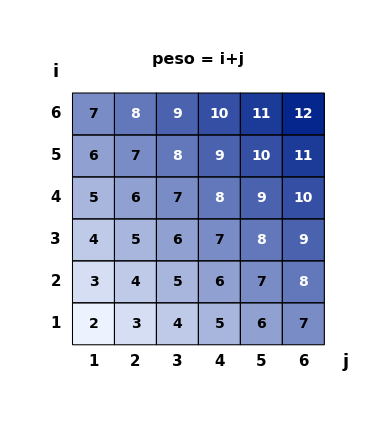
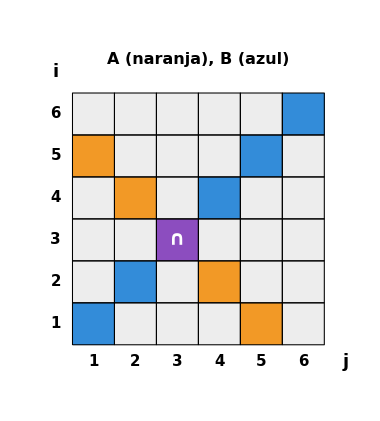
-Graphics-
c = 252-Graphics-


Resumen del apartado c):
P(A) = 5/42
P(B) = 1/6
P(A∩B) = 1/42
P(C) = P(AΔB) = P(A)+P(B)-2P(A∩B) = 5/21

```mathematica
nCaras=6;

(* ======================Valores dados directamente en la resolución (sin calcular nada)======================*)

(*Matriz de pesos i+j,escrita explícitamente fila a fila (fila=i,columna=j)*)
matrizPesos={{2,3,4,5,6,7},{3,4,5,6,7,8},{4,5,6,7,8,9},{5,6,7,8,9,10},{6,7,8,9,10,11},{7,8,9,10,11,12}};

c=252; (*apartado a)*)

A={{1,5},{2,4},{3,3},{4,2},{5,1}}; (*suceso A:suma=6*)
B={{1,1},{2,2},{3,3},{4,4},{5,5},{6,6}}; (*suceso B:resultados iguales*)

PA=5/42;
PB=1/6;
PAB=1/42;
PC=5/21;

(* ======================PANEL 1:mapa de calor de los pesos i+j======================*)
colorHeat[v_]:=Blend[{RGBColor[0.93,0.95,1],RGBColor[0.02,0.15,0.55]},(v-2)/10];

ejesGrilla[titulo_]:={Table[Text[Style[j,15,Bold],{j-0.5,-0.4}],{j,1,nCaras}],Table[Text[Style[i,15,Bold],{-0.4,i-0.5}],{i,1,nCaras}],Text[Style["j",18,Bold],{nCaras+0.5,-0.4}],Text[Style["i",18,Bold],{-0.4,nCaras+0.5}],Text[Style[titulo,16,Bold],{nCaras/2.,nCaras+0.8}]};

cellsHeat=Table[{colorHeat[matrizPesos[[i,j]]],EdgeForm[{Black,Thickness[0.002]}],Rectangle[{j-1,i-1},{j,i}]},{i,1,nCaras},{j,1,nCaras}];

textHeat=Table[Text[Style[matrizPesos[[i,j]],14,Bold,If[matrizPesos[[i,j]]>=8,White,Black]],{j-0.5,i-0.5}],{i,1,nCaras},{j,1,nCaras}];

panel1Graf=Graphics[{cellsHeat,textHeat,ejesGrilla["peso = i+j"]},PlotRange->{{-0.9,nCaras+0.5},{-0.9,nCaras+1.3}},ImageSize->380];

panel1=Column[{panel1Graf,Style["c = "<>ToString[c],16,Bold]},Alignment->Center];

(* ======================PANEL 2:sucesos A,B y su diferencia simétrica C======================*)
colorOnlyA=RGBColor[0.95,0.6,0.15];   (*solo A:suma=6*)
colorOnlyB=RGBColor[0.2,0.55,0.85];   (*solo B:i=j*)
colorBoth=RGBColor[0.55,0.3,0.75];    (*A∩B*)
colorNone=RGBColor[0.93,0.93,0.93];   (*ninguno*)

cellColor[i_,j_]:=Which[MemberQ[A,{i,j}]&&MemberQ[B,{i,j}],colorBoth,MemberQ[A,{i,j}],colorOnlyA,MemberQ[B,{i,j}],colorOnlyB,True,colorNone];

cellsSets=Table[{cellColor[i,j],EdgeForm[{Black,Thickness[0.002]}],Rectangle[{j-1,i-1},{j,i}]},{i,1,nCaras},{j,1,nCaras}];

marcaInterseccion=Table[If[MemberQ[A,{i,j}]&&MemberQ[B,{i,j}],Text[Style["∩",20,Bold,White],{j-0.5,i-0.5}],{}],{i,1,nCaras},{j,1,nCaras}];

panel2Graf=Graphics[{cellsSets,marcaInterseccion,ejesGrilla["A (naranja), B (azul)"]},PlotRange->{{-0.9,nCaras+0.5},{-0.9,nCaras+1.3}},ImageSize->380];

leyendaSets=SwatchLegend[{colorOnlyA,colorOnlyB,colorBoth,colorNone},{"A∖B (suma=6, i≠j)","B∖A (i=j, suma≠6)","A∩B = {(3,3)}","ninguno"},LabelStyle->Directive[FontSize->15],LegendMarkerSize->18];

panel2=Column[{panel2Graf,leyendaSets},Alignment->Center];

(* ======================Composición final con resumen numérico (valores dados,no calculados)======================*)
diagramaCompleto=Row[{panel1,Spacer[50],panel2}];

resumen=Column[{Row[{Style["P(A) = ",16],Style["5/42",16,Bold,colorOnlyA]}],Row[{Style["P(B) = ",16],Style["1/6",16,Bold,colorOnlyB]}],Row[{Style["P(A∩B) = ",16],Style["1/42",16,Bold,colorBoth]}],Row[{Style["P(C) = P(AΔB) = P(A)+P(B)-2P(A∩B) = ",16],Style["5/21",16,Bold,Darker[Red]]}]},Alignment->Left,Spacings->0.8];

imagenFinal=Column[{diagramaCompleto,Spacer[15],Style["Resumen del apartado c):",18,Bold],resumen},Alignment->Center];

imagenFinal
```

```mathematica
Export["prob_quesada_2_15_a.png",imagenFinal,Background->White,ImageResolution->300];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["prob_quesada_2_15_a.png"]]]
```